# 1)Phase transition of gapless QSL for M=0 case.

In this notebook, I investigate the topological phase transition from a gapless quantum spin liquid to a gapped quantum spin liquid. In this case M=0, λ also goes to 0. Hence the eigenvalues of the Hamiltonian simply become: 

ϵ_(1,±)=±|γ_0|
ϵ_(2,±)=±|γ_z|
ϵ_(3,±)=±|γ_x|
ϵ_(4,±)=±|γ_y|

This makes the calculations significantly shorter.
In this calculation we must define an integral over the Brillouin Zone, we can test this, 1 integrated over the Brillouin Zone divided by the Brillouin Zone area must be 1.

```mathematica
(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[1,{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[1,{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[1,{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
```

```mathematica
0.9999999999999998
```

1.

Now we will define the Lattice vectors:

a_1==(-(√3)/2,3/2)
a_2==((√3)/2,3/2)

We dot product these with reciprocal lattice vectors k==(k_x,k_y), we denote k_x and k_y as kx and ky respectively:
n_i = (k_x,k_y). a_i

```mathematica
Clear[kx];
Clear[ky];
n1[kx_,ky_]:=-kx*Sqrt[3]/2+(3/2)*ky
n2[kx_,ky_]:=kx*Sqrt[3]/2+(3/2)*ky
```

Now we must define the Dispersion relations, these are defined as:

-Graphics-

Will will calculated the magnitude of these by writing the imaginary numbers in Euler form to cos(θ)+ i*sin(θ) form.

-Graphics-
Now we will type these formula into Mathematica as functions. 

variable - Mathematica Variable label
c_z - Cz
c_⊥ - Cp
B_⊥ - Bp
B_z - Bz

```mathematica
gamma0mag[Cp_,Cz_,kx_,ky_]:= Sqrt[(Cz+Cp*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2 + (Cp*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaZmag[Bp_,Bz_,P1_,P_,K1_,kx_,ky_] := Sqrt[((1+P+K1*(1+P1))*Bz+Bp*K1*(1+P1)*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+(Bp*K1*(1+P1)*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaXmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n1[kx,ky]]+K1*Cos[n2[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n1[kx,ky]]+K1*Sin[n2[kx,ky]]))^2]

gammaYmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n2[kx,ky]]+K1*Cos[n1[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n2[kx,ky]]+K1*Sin[n1[kx,ky]]))^2]
E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)

Eigensum[P1_,P_,K1_,A1_,A2_,Bp_,Bz_,kx_,ky_]:= gamma0mag[A1,A2,kx,ky]+gammaZmag[Bp,Bz,P1,P,K1,kx,ky]+gammaXmag[P1,K1,Bp,Bz,kx,ky]+gammaYmag[P1,K1,Bp,Bz,kx,ky]
```

The energy of this system is given by the function:

```mathematica
Energy [P1_,P_,K1_,Cz_,Cp_,Bp_,Bz_]:= -1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}])+E0[P1,K1,P,0,Bp,Bz,Cp,Cz]
```

We calculate the derivatives of the eigensum with respect to A_1,A_2,B_z,B_⊥ and store them as functions. These will be integrated over the Brillouin zone iteratively to find the mean field parameters that minimise the energy, i.e to find the ground state energy.

```mathematica
Clear[Bp];
Clear[Bz];
Clear[Cp];
Clear[Cz];
FBp[kx_,ky_,rho_,rho1_,kappa_,i_]:=(D[Eigensum[rho1,rho,kappa,cp[[i]],cz[[i]],Bp,bz[[i]],kx,ky],Bp]/. Bp->bp[[i]]);
FBz[kx_,ky_,rho_,rho1_,kappa_,i_]:= (D[Eigensum[rho1,rho,kappa,cp[[i]],cz[[i]],bp[[i]],Bz,kx,ky],Bz]/. Bz->bz[[i]]);
FCp[kx_,ky_,rho_,rho1_,kappa_,i_]:= (D[Eigensum[rho1,rho,kappa,Cp,cz[[i]],bp[[i]],bz[[i]],kx,ky],Cp]/. Cp->cp[[i]]);
FCz[kx_,ky_,rho_,rho1_,kappa_,i_]:=(D[Eigensum[rho1,rho,kappa,cp[[i]], Cz,bp[[i]],bz[[i]],kx,ky],Cz]/. Cz->cz[[i]]);
```

## Test case for one ρ̃=0, ρ=1,κ=0:

$Aborted

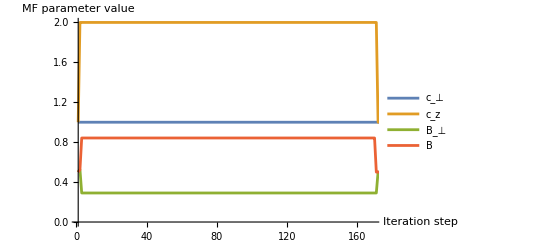

c_⊥ =1., c_z=2., B_⊥=0.290901TraditionalForm`0.842053

r=2.

```mathematica
(*Define the anisotropy and set magnetisation to 0*)
P1=0;
P=1;
K1=0;
M=0;
L=0;
(*define the number of times we iterate over to find the mean field parameters*)
loop=200;

cp = ConstantArray[1,loop];(*Array to store the mean field parameters with each iteration step*)
cz = ConstantArray[1,loop];
bp=ConstantArray[0.5,loop];
bz=ConstantArray[0.5,loop];

For[i=1,i<loop,i++, (*Loop in which the 4 MF parameters are iterated over*)
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);


bp[[i+1]] =(1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
final=i;
]

(*plot of the mean field parameters over each iteration step*)
ListLinePlot[{cp,cz,bp,bz},PlotLegends->{"c_⊥ ","c_z","B_⊥","B"},PlotRange->{{1,final},Automatic}, AxesLabel->{"Iteration step", "MF parameter value"}]
(*Print the final value of the MF parameters and the r value*)
Print["c_⊥ =",cp[[final]] ,", c_z=",cz[[final]],", B_⊥=", bp[[final]],"TraditionalForm`", bz[[final]]]
Print["r=",cz[[final]]/cp[[final]]]
```

A plot of the energy spectrum as a function of momentum

## Dispersion band plot of η^x and η^y

```mathematica
Plot3D[{ gamma0mag[cp[[final]],cz[[final]],kx,ky],gammaZmag[bp[[final]],bz[[final]],P1,P,K1,kx,ky],-gamma0mag[cp[[final]],cz[[final]],kx,ky],-gammaZmag[bp[[final]],bz[[final]],P1,P,K1,kx,ky]},{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->25, AspectRatio->0.75, AxesLabel->{Style["K_x",15,Bold],Style["K_y",15,Bold], Style["ϵ",15,Bold]}]
```

-Graphics3D-

Now plotting the energy with each iteration step.

## Dispersion band plot of η^x and η^y

```mathematica
Plot3D[{ gammaXmag[P1,K1,bp[[final]],bz[[final]],kx,ky], gammaYmag[P1,K1,bp[[final]],bz[[final]],kx,ky],-gammaXmag[P1,K1,bp[[final]],bz[[final]],kx,ky], -gammaYmag[P1,K1,bp[[final]],bz[[final]],kx,ky]},{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->50, AspectRatio->0.75, AxesLabel->{Style["K_x",15,Bold],Style["K_y",15,Bold], Style["ϵ",15,Bold]}]
```

-Graphics3D-

## Contour plot of η^0 dispersion band:

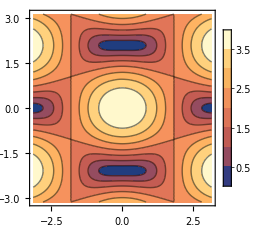

```mathematica
ContourPlot[ gamma0mag[cp[[final]],cz[[final]],kx,ky],{kx,-Pi,Pi},{ky,-Pi, Pi},PlotLegends->Automatic]
```

## Energy Plot for each iteration step:

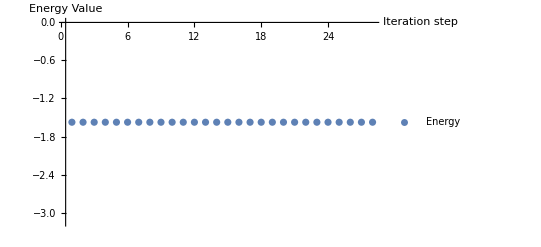

-1.5746

```mathematica
Energyval=ConstantArray[0,final-1];
For[n=1,n<final,n++,
Energyval[[n]] = Energy [P1,P,K1,cp[[n]],cz[[n]],bp[[n]],bz[[n]]]
]
ListPlot[Energyval,PlotRange->Full,PlotLegends->{"Energy"}, AxesLabel->{"Iteration step", "Energy Value"}]
If[Energyval[[final-2]]*0.9999<=Energyval[[final-2]]<=Energyval[[final-2]]*1.0001,
Print["Energy has converged, the converged energy value is "]
]
Print[ Energyval[[final-1]]]
```

# 2)Checking the continuity of r:

We will check the continuity of r varying ρ :

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

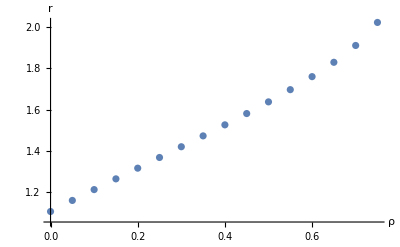

```mathematica
P1=0.8; (*First define the anisotropy parameters that are kept constant*)
K1=0.25; 
M=0;
L=0;
loop=10;(*Define the number of iterations over which the MF parameters are calculated given some anisotropy parameters*)

rval=Range[0,0.75,0.05]; (*stores the value of r for some given anistropy parameters*)
rhoval=Range[0,0.75,0.05];(*The values for anisotropy in the Kitaev model over which we calculate r*)
cpg=1; (*Initial guess for the ρ=0 case*)
czg=1;
bpg=0.5;
bzg=0.5;

For[j=1,j<=Length[rhoval],j++, (*loop to iterate over each ρ value*)
P=rhoval[[j]];
cp = ConstantArray[cpg,loop]; (*arrays to store the MF parameters as we iterate*)
cz = ConstantArray[czg,loop];
bp=ConstantArray[bpg,loop];
bz=ConstantArray[bzg,loop];
For[i=1,i<loop,i++,(*loop to minimise energy and calculate the MF parameters given some value of ρ*)
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBz[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);


bp[[i+1]] =(1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCp[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCz[kx,ky,P,P1,K1,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
final=i;
];
rval[[j]]=cz[[final]]/cp[[final]];(*value of r given Subscript[ρ, j] which is stored*)
cpg=cp[[final]];
czg=cz[[final]];
bpg=bp[[final]];
bzg=bz[[final]]; (*The initial guesses for the calculation for the guesses for the MF parameters for the next Subscript[ρ, j+1] value is the final MF parameters calculated for Subscript[ρ, j]*)

]

ListPlot[Transpose[{Take[rhoval,j-1],Take[rval,j-1]}], PlotRange->Automatic, AxesLabel->{"ρ","r"}]
```

we can see for values up to ρ̃=0.8 we can see r is continuous across r=2, up to κ=0.25.
I have not checked for ρ̃>0.8

# 3) Using bisection to find the topological phase transition:

```mathematica
(*ρ̃*)P1=0;
Kappaval=Range[0,0.25,0.01]; (*set of κ values for which the topological phase transition is calculated for*)
coords1 = ConstantArray[10,Length[Kappaval]]; (*stores the value of ρ and κ at which topological phase transition occurs*)
loop=30;(*number of iterations the MF parameters are calculated over given some ρ and κ*)
For[k=1,k<=Length[Kappaval],k++,(*Loop over the different κ values*)
Pmin=0;
Pmax=1.5;
For[j=1,j<=10,j++,(*loop over which we perform the bisection given some κ value*)
p0=(Pmax+Pmin)/2; 
cp = ConstantArray[1,loop];(*as we iterate to calculate the MF parameters given some κ and ρ, determined by bisection, we use store them in these arrays*)
cz = ConstantArray[1,loop];
bp=ConstantArray[0.5,loop];
bz=ConstantArray[0.5,loop];
For[i=1,i<loop,i++,
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,p0,P1,Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FCp[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCp[kx,ky,p0,P1,Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCp[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FCz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCz[kx,ky,p0,P1,Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
final=i;
];
r=cz[[final]]/cp[[final]];

If[r==2,j=10]; (*The three conditional statements are responsible for bisection*)
If[r<2,Pmin=p0];
If[r>2,Pmax=p0];


];
coords1[[k]]= {Kappaval[[k]],p0} (*stores the coordinates at which the topological phase transition occurs, i.e the value of ρ and κ at which r=2*)
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

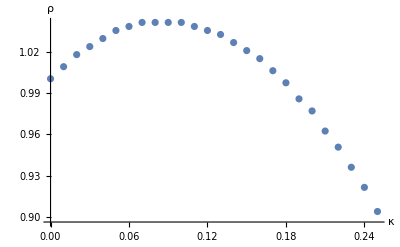

InterpolatingFunction[…]

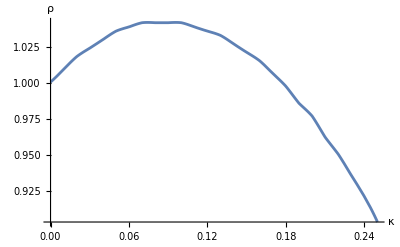

```mathematica
ListPlot[coords1,AxesLabel->{Style["κ",13],Style["ρ",13,Bold]},PlotRange->Full]
f=Interpolation[coords1]
Plot[f[x],{x,0,0.25},AxesLabel->{Style["κ",13],Style["ρ",13,Bold]}]
```

# 3) Using bisection to find the topological phase transition at different ρ̃:

The code is identical to before, however now we iterate over different ρ̃ values

```mathematica
Kappaval=Range[0,0.25,0.01];
Rhobarval=Range[0,0.8,0.2];
coords2 = ConstantArray[10,Length[Kappaval]*Length[Rhobarval]];
loop=30;

For[l=1,l<=Length[Rhobarval],l++,(*loop for different values of ρ̃*)
For[k=1,k<=Length[Kappaval],k++,(*loop for different values of κ*)
Pmin=0;
Pmax=1.5;
For[j=1,j<=10,j++,(*loop for bisection*)
p0=(Pmax+Pmin)/2;
cp = ConstantArray[1,loop];
cz = ConstantArray[1,loop];
bp=ConstantArray[0.5,loop];
bz=ConstantArray[0.5,loop];
For[i=1,i<loop,i++,(*loop to calculate the MF parameters given some κ,ρ̃,ρ*)
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FCp[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCp[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCp[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FCz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FCz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FCz[kx,ky,p0,Rhobarval[[l]],Kappaval[[k]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
final=i;
];
r=cz[[final]]/cp[[final]];

If[r==2,j=10];
If[r<2,Pmin=p0];
If[r>2,Pmax=p0];
];
coords2[[k+(l-1)*Length[Kappaval]]]= {Rhobarval[[l]],Kappaval[[k]],p0}(*Store the coordinates from bisection for which r=2*)
]
]
```

```mathematica
coords2(*print the coordinates*)
```

{{0.,0.,1.00049},{0.,0.01,1.00928},{0.,0.02,1.01807},{0.,0.03,1.02393},{0.,0.04,1.02979},{0.,0.05,1.03564},{0.,0.06,1.03857},{0.,0.07,1.0415},{0.,0.08,1.0415},{0.,0.09,1.0415},{0.,0.1,1.0415},{0.,0.11,1.03857},{0.,0.12,1.03564},{0.,0.13,1.03271},{0.,0.14,1.02686},{0.,0.15,1.021},{0.,0.16,1.01514},{0.,0.17,1.00635},{0.,0.18,0.997559},{0.,0.19,0.98584},{0.,0.2,0.977051},{0.,0.21,0.962402},{0.,0.22,0.950684},{0.,0.23,0.936035},{0.,0.24,0.921387},{0.,0.25,0.903809},{0.2,0.,1.00049},{0.2,0.01,1.00635},{0.2,0.02,1.01221},{0.2,0.03,1.01807},{0.2,0.04,1.021},{0.2,0.05,1.02393},{0.2,0.06,1.02686},{0.2,0.07,1.02686},{0.2,0.08,1.02686},{0.2,0.09,1.02393},{0.2,0.1,1.021},{0.2,0.11,1.01807},{0.2,0.12,1.01221},{0.2,0.13,1.00635},{0.2,0.14,1.00049},{0.2,0.15,0.991699},{0.2,0.16,0.98291},{0.2,0.17,0.974121},{0.2,0.18,0.962402},{0.2,0.19,0.950684},{0.2,0.2,0.938965},{0.2,0.21,0.924316},{0.2,0.22,0.909668},{0.2,0.23,0.89502},{0.2,0.24,0.877441},{0.2,0.25,0.859863},{0.4,0.,1.00049},{0.4,0.01,1.00635},{0.4,0.02,1.00928},{0.4,0.03,1.01221},{0.4,0.04,1.01514},{0.4,0.05,1.01514},{0.4,0.06,1.01514},{0.4,0.07,1.01221},{0.4,0.08,1.01221},{0.4,0.09,1.00635},{0.4,0.1,1.00342},{0.4,0.11,0.997559},{0.4,0.12,0.991699},{0.4,0.13,0.98291},{0.4,0.14,0.974121},{0.4,0.15,0.965332},{0.4,0.16,0.953613},{0.4,0.17,0.941895},{0.4,0.18,0.930176},{0.4,0.19,0.918457},{0.4,0.2,0.903809},{0.4,0.21,0.88623},{0.4,0.22,0.871582},{0.4,0.23,0.854004},{0.4,0.24,0.833496},{0.4,0.25,0.815918},{0.6,0.,1.00049},{0.6,0.01,1.00342},{0.6,0.02,1.00635},{0.6,0.03,1.00635},{0.6,0.04,1.00635},{0.6,0.05,1.00635},{0.6,0.06,1.00342},{0.6,0.07,1.00049},{0.6,0.08,0.994629},{0.6,0.09,0.991699},{0.6,0.1,0.98291},{0.6,0.11,0.977051},{0.6,0.12,0.968262},{0.6,0.13,0.959473},{0.6,0.14,0.947754},{0.6,0.15,0.938965},{0.6,0.16,0.924316},{0.6,0.17,0.912598},{0.6,0.18,0.897949},{0.6,0.19,0.883301},{0.6,0.2,0.868652},{0.6,0.21,0.851074},{0.6,0.22,0.833496},{0.6,0.23,0.812988},{0.6,0.24,0.79248},{0.6,0.25,0.771973},{0.8,0.,1.00049},{0.8,0.01,1.00049},{0.8,0.02,1.00049},{0.8,0.03,1.00049},{0.8,0.04,0.997559},{0.8,0.05,0.994629},{0.8,0.06,0.991699},{0.8,0.07,0.98584},{0.8,0.08,0.97998},{0.8,0.09,0.974121},{0.8,0.1,0.965332},{0.8,0.11,0.956543},{0.8,0.12,0.947754},{0.8,0.13,0.936035},{0.8,0.14,0.924316},{0.8,0.15,0.909668},{0.8,0.16,0.897949},{0.8,0.17,0.883301},{0.8,0.18,0.865723},{0.8,0.19,0.851074},{0.8,0.2,0.833496},{0.8,0.21,0.812988},{0.8,0.22,0.79541},{0.8,0.23,0.774902},{0.8,0.24,0.751465},{0.8,0.25,0.730957}}

I store the coordinates so I do not have to recompute these every time I start the code again.

```mathematica
coords2 ={{0.,0.,1.00048828125},{0.,0.01,1.00927734375},{0.,0.02,1.01806640625},{0.,0.03,1.02392578125},{0.,0.04,1.02978515625},{0.,0.05,1.03564453125},{0.,0.06,1.03857421875},{0.,0.07,1.04150390625},{0.,0.08,1.04150390625},{0.,0.09,1.04150390625},{0.,0.1,1.04150390625},{0.,0.11,1.03857421875},{0.,0.12,1.03564453125},{0.,0.13,1.03271484375},{0.,0.14,1.02685546875},{0.,0.15,1.02099609375},{0.,0.16,1.01513671875},{0.,0.17,1.00634765625},{0.,0.18,0.99755859375},{0.,0.19,0.98583984375},{0.,0.2,0.97705078125},{0.,0.21,0.96240234375},{0.,0.22,0.95068359375},{0.,0.23,0.93603515625},{0.,0.24,0.92138671875},{0.,0.25,0.90380859375},{0.2,0.,1.00048828125},{0.2,0.01,1.00634765625},{0.2,0.02,1.01220703125},{0.2,0.03,1.01806640625},{0.2,0.04,1.02099609375},{0.2,0.05,1.02392578125},{0.2,0.06,1.02685546875},{0.2,0.07,1.02685546875},{0.2,0.08,1.02685546875},{0.2,0.09,1.02392578125},{0.2,0.1,1.02099609375},{0.2,0.11,1.01806640625},{0.2,0.12,1.01220703125},{0.2,0.13,1.00634765625},{0.2,0.14,1.00048828125},{0.2,0.15,0.99169921875},{0.2,0.16,0.98291015625},{0.2,0.17,0.97412109375},{0.2,0.18,0.96240234375},{0.2,0.19,0.95068359375},{0.2,0.2,0.93896484375},{0.2,0.21,0.92431640625},{0.2,0.22,0.90966796875},{0.2,0.23,0.89501953125},{0.2,0.24,0.87744140625},{0.2,0.25,0.85986328125},{0.4,0.,1.00048828125},{0.4,0.01,1.00634765625},{0.4,0.02,1.00927734375},{0.4,0.03,1.01220703125},{0.4,0.04,1.01513671875},{0.4,0.05,1.01513671875},{0.4,0.06,1.01513671875},{0.4,0.07,1.01220703125},{0.4,0.08,1.01220703125},{0.4,0.09,1.00634765625},{0.4,0.1,1.00341796875},{0.4,0.11,0.99755859375},{0.4,0.12,0.99169921875},{0.4,0.13,0.98291015625},{0.4,0.14,0.97412109375},{0.4,0.15,0.96533203125},{0.4,0.16,0.95361328125},{0.4,0.17,0.94189453125},{0.4,0.18,0.93017578125},{0.4,0.19,0.91845703125},{0.4,0.2,0.90380859375},{0.4,0.21,0.88623046875},{0.4,0.22,0.87158203125},{0.4,0.23,0.85400390625},{0.4,0.24,0.83349609375},{0.4,0.25,0.81591796875},{0.6000000000000001,0.,1.00048828125},{0.6000000000000001,0.01,1.00341796875},{0.6000000000000001,0.02,1.00634765625},{0.6000000000000001,0.03,1.00634765625},{0.6000000000000001,0.04,1.00634765625},{0.6000000000000001,0.05,1.00634765625},{0.6000000000000001,0.06,1.00341796875},{0.6000000000000001,0.07,1.00048828125},{0.6000000000000001,0.08,0.99462890625},{0.6000000000000001,0.09,0.99169921875},{0.6000000000000001,0.1,0.98291015625},{0.6000000000000001,0.11,0.97705078125},{0.6000000000000001,0.12,0.96826171875},{0.6000000000000001,0.13,0.95947265625},{0.6000000000000001,0.14,0.94775390625},{0.6000000000000001,0.15,0.93896484375},{0.6000000000000001,0.16,0.92431640625},{0.6000000000000001,0.17,0.91259765625},{0.6000000000000001,0.18,0.89794921875},{0.6000000000000001,0.19,0.88330078125},{0.6000000000000001,0.2,0.86865234375},{0.6000000000000001,0.21,0.85107421875},{0.6000000000000001,0.22,0.83349609375},{0.6000000000000001,0.23,0.81298828125},{0.6000000000000001,0.24,0.79248046875},{0.6000000000000001,0.25,0.77197265625},{0.8,0.,1.00048828125},{0.8,0.01,1.00048828125},{0.8,0.02,1.00048828125},{0.8,0.03,1.00048828125},{0.8,0.04,0.99755859375},{0.8,0.05,0.99462890625},{0.8,0.06,0.99169921875},{0.8,0.07,0.98583984375},{0.8,0.08,0.97998046875},{0.8,0.09,0.97412109375},{0.8,0.1,0.96533203125},{0.8,0.11,0.95654296875},{0.8,0.12,0.94775390625},{0.8,0.13,0.93603515625},{0.8,0.14,0.92431640625},{0.8,0.15,0.90966796875},{0.8,0.16,0.89794921875},{0.8,0.17,0.88330078125},{0.8,0.18,0.86572265625},{0.8,0.19,0.85107421875},{0.8,0.2,0.83349609375},{0.8,0.21,0.81298828125},{0.8,0.22,0.79541015625},{0.8,0.23,0.77490234375},{0.8,0.24,0.75146484375},{0.8,0.25,0.73095703125}};
```

```mathematica
Plotting the curve of ρ vs κ for different ρ̃
```

I will now use the previously defined coorindate array to plot the topological phase transition for different ρ̃, there are 25 array points for each

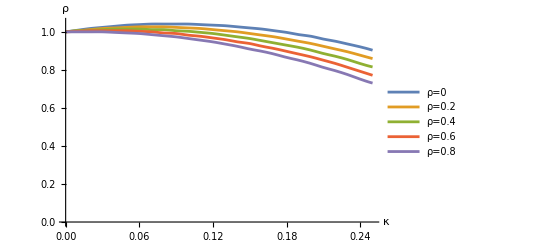

```mathematica
(*ρ̃=0*)
coordinates=coords2; 
x1 = Take[(Transpose[coordinates][[2]]),{1,26}];(*take the first 25 elements of the array defined above, corresponding to ρ̃=0*)
y1 = Take[(Transpose[coordinates][[3]]),{1,26}];
f1= Interpolation[Transpose[{x1,y1}]]; (*interpolate over these coordinates.*)
(*ρ̃=0.2*)
x2 = Take[(Transpose[coordinates][[2]]),{27,52}];
y2 = Take[(Transpose[coordinates][[3]]),{27,52}];
f2 = Interpolation[Transpose[{x2,y2}]];
(*ρ̃=0.4*)
x3 = Take[(Transpose[coordinates][[2]]),{53,78}];
y3 = Take[(Transpose[coordinates][[3]]),{53,78}];
f3 = Interpolation[Transpose[{x3,y3}]];
(*ρ̃=0.6*)
x4 = Take[(Transpose[coordinates][[2]]),{79,104}];
y4 = Take[(Transpose[coordinates][[3]]),{79,104}];
f4= Interpolation[Transpose[{x4,y4}]];
(*ρ̃=0.8*)
x5 = Take[(Transpose[coordinates][[2]]),{105,130}];
y5 = Take[(Transpose[coordinates][[3]]),{105,130}];
f5= Interpolation[Transpose[{x5,y5}]];

Plot[{f1[x],f2[x],f3[x],f4[x],f5[x]},{x,0,0.25},PlotRange->{{0,1.05}},PlotLegends->{"ρ=0","ρ=0.2","ρ=0.4","ρ=0.6","ρ=0.8",},AxesLabel->{Style["κ",15],Style["ρ",15,Bold]}]
```